From Bensoussan 1982

```mathematica
Exit[]
```

```mathematica
σ={{x[1] Σ[x[2]] v,0},{Σ[x[2]],0}};
```

```mathematica
H=-Sum[K[i,j]σ[[i,j]],{i,2},{j,2}]
```

-K[2,1] Σ[x[2]]-v K[1,1] x[1] Σ[x[2]]

```mathematica
D[H,v]
```

-K[1,1] x[1] Σ[x[2]]

```mathematica
(*  K[1,1]:  *)
Simplify[Sum[D[σ[[1,1]],x[b]]p[b]-ψ[b,1]G[b,1],{b,2}]]
```

v p[1] Σ[x[2]]-G[1,1] ψ[1,1]-G[2,1] ψ[2,1]+v p[2] x[1] Σ'[x[2]]

```mathematica
(*  K[1,2]:  *)
Simplify[Sum[D[σ[[1,2]],x[b]]p[b]-ψ[b,1]G[b,2],{b,2}]]
```

-G[1,2] ψ[1,1]-G[2,2] ψ[2,1]

```mathematica
(*  p:  *)
Simplify[Table[Sum[D[σ[[i,j]],x[a]]K[a,j],{a,2},{j,2}],{i,2}]]
```

{v (K[1,1] Σ[x[2]]+K[2,1] x[1] Σ'[x[2]]),K[2,1] Σ'[x[2]]}

```mathematica
(*  ϕ[1,j]:  *)
Simplify[Table[Sum[D[σ[[1,i]],x[n]]ϕ[n,j]dW[i],{i,2},{n,2}],{j,2}]]
```

{v dW[1] (Σ[x[2]] ϕ[1,1]+x[1] ϕ[2,1] Σ'[x[2]]),v dW[1] (Σ[x[2]] ϕ[1,2]+x[1] ϕ[2,2] Σ'[x[2]])}

```mathematica
h//MatrixForm
```

(0 | 0 | 0
0 | q1 u σ^(2,0)[S,t] | q1 σ^(1,0)[S,t]
0 | q1 σ^(1,0)[S,t] | 0)

```mathematica
Simplify[Det[h]]
```

0

```mathematica
Simplify[Eigenvalues[h]]
```

{0,1/2 (q1 u σ^(2,0)[S,t]-q1 √(4 (σ^(1,0)[S,t])^2+u^2 (σ^(2,0)[S,t])^2)),1/2 q1 (u σ^(2,0)[S,t]+√(4 (σ^(1,0)[S,t])^2+u^2 (σ^(2,0)[S,t])^2))}

```mathematica
Simplify[Det[h]]
```

-q1^2 u^2 (σ^(1,0)[S,t])^2

```mathematica
g[P_]:=-HeavisideTheta[Exp[P]-m]*(Exp[P]-m)
```

```mathematica
D[-g[Log[p]],p]
```

(-m+p) DiracDelta[-m+p]+HeavisideTheta[-m+p]

```mathematica
D[g[P],P]
```

-ⅇ^P (ⅇ^P-m) DiracDelta[ⅇ^P-m]-ⅇ^P HeavisideTheta[ⅇ^P-m]

```mathematica
D[g[P],P]/.m->1
```

-ⅇ^P (-1+ⅇ^P) DiracDelta[-1+ⅇ^P]-ⅇ^P HeavisideTheta[-1+ⅇ^P]

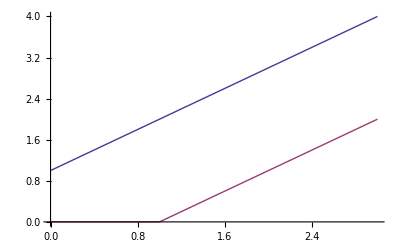

```mathematica
Plot[{1(P+1),-g[Log[P]]/.m->1},{P,0,3}]
```

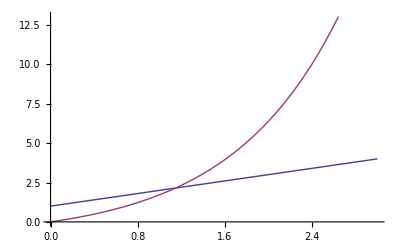

```mathematica
Plot[{1(P+1),-g[P]/.m->1},{P,0,3}]
```

```mathematica
h=HessianH[ σ[S,t] u q1,{P,S}]
```

{{0,0},{0,q1 u σ^(2,0)[S,t]}}

```mathematica
Eigenvalues[h]
```

{0,q1 u σ^(2,0)[S,t]}

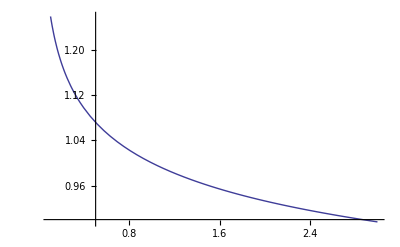

```mathematica
Plot[S^(0.9-1),{S,0.1,3}]
```

```mathematica
Simplify[D[S^(b-1),S,S]/ S^(-3+b)]
```

(-2+b) (-1+b)

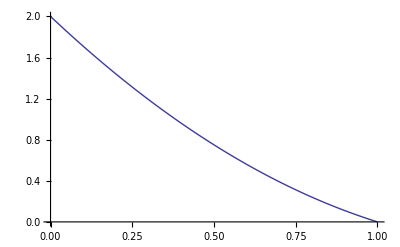

```mathematica
Plot[(-2+b) (-1+b),{b,0,1}]
```